# Original Optimization Principle

In words:
Take all the singular values above the threshold “t” and discount them by the threshold “t”

```mathematica
{m,n}={11,23};
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
σs=Diagonal[S];r=Length[σs];
Norm[A-U.S.Vᵀ];

vars=Table[s[i],{i,1,r}];
t=3; rOpt=Count[Sign[σs-t],1];
{MinVal,MinArg}=Minimize[ {
0.5(vars-σs).(vars-σs) +t Total[vars],
vars>0},vars] ;
{MinVal,MinArg=Chop[vars/.MinArg,10^-7]};
TableForm[{MinArg,Join[Table[σs⟦i⟧-t,{i,1,rOpt}],ConstantArray[0,r-rOpt]]},
TableHeadings->{{"Numerical","Analytical"},Automatic}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
Numerical | 2.21334 | 0.717771 | 0.475324 | 0.0690667 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Analytical | 2.21334 | 0.717771 | 0.475324 | 0.0690667 | 0 | 0 | 0 | 0 | 0 | 0 | 0

# Constrained Optimization Principle ||B(||)_F≥β^2

In words:
Take all the singular values above the threshold and discount them by the threshold “t”, call the vector v.  If ||v||≥β otherwise scale v so that ||α v||=β

```mathematica
{m,n}={11,23};
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
σs=Diagonal[S];r=Length[σs];
Norm[A-U.S.Vᵀ];

vars=Table[s[i],{i,1,r}];
t=3;β=1.6^2; rOpt=Count[Sign[σs-t],1];
{MinVal,MinArg}=Minimize[ {
0.5(vars-σs).(vars-σs) +t Total[vars],
{vars>0,0.5 vars.vars>β}},vars] ;
{MinVal,MinArg=Chop[vars/.MinArg,10^-7]};
Ss=Join[Table[σs⟦i⟧-t,{i,1,rOpt}],ConstantArray[0,r-rOpt]];
α=√(β/(0.5 Ss.Ss));
Ss=α Ss
TableForm[{MinArg,Ss},
TableHeadings->{{"Numerical","Analytical"},Automatic}]
```

{1.95366,1.06025,0.366794,0.211086,0.,0.,0.,0.,0.,0.,0.}

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
Numerical | 1.95366 | 1.06025 | 0.366795 | 0.211087 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Analytical | 1.95366 | 1.06025 | 0.366794 | 0.211086 | 0. | 0. | 0. | 0. | 0. | 0. | 0.

# Constrained Optimization Principle ||B(||)_*≥β

In words:
1) Find the modified threshold s.  
	a) If β is small.  The test is β≤+∑_(σ ≥ t) σ.   
	This case the opt is an interior critical point.  
	The constraint it inactive and the just the penalization t as before.  The solution involves only singular values above “t”.
	b) If ∑_(σ ≥ t) σ≤β≤∑σ the constraint is active but only involves the singular values above a different threshold.  Specifically,
	define r to be the index satisfying
		∑_(i=1)^r σ_i≤β≤∑_(i=1)^(r+1) σ_i 
	Then the solution only involves the singular values σ_1≥σ_2≥…≥σ_r and the penalization is just enough to satisfy
		∑_(i=1)^r (σ_i-s)=β   
	c) If β is big. The test is β≥∑σ. 
	In this case the penalization is active and the solution involves all the singular values 
2) Take all the singular values above the modified threshold s and discount them by the modified threshold “s”

```mathematica
{m,n}={5,9}; 
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
σs=Diagonal[S];rMax=Length[σs]; 
 t=0.9;
PartialNuclearNorms=Accumulate[σs]
β=3.8;
σ=SelectFirst[PartialNuclearNorms,(#>β)&]
Switch[σ,
Missing["NotFound"], Print["New Case: All Singular Values"];σs+(β-PartialNuclearNorms⟦rMax⟧)/rMax,
σs⟦1⟧, Print["Old Case"];Map[Max[#,0]&, σs-t],
_,Print["Last Case"]; r=Position[PartialNuclearNorms,σ]⟦1,1⟧ +1; σs⟦1;;r⟧-(β-PartialNuclearNorms⟦r⟧)/r
]

vars=Table[s[i],{i,1,rMax}];
{MinVal,MinArg}=Minimize[ {
0.5(vars-σs).(vars-σs) +t Total[vars],
{vars>0,Total[vars]>β}},vars] ;
{MinVal,MinArg=Chop[vars/.MinArg,10^-7]}
```

{2.39936,4.60293,6.29643,7.4586,8.43906}

4.60293

Last Case

{3.2315,3.03572,2.52564}

{5.57015,{1.49936,1.30357,0.793496,0.26217,0.0804632}}

```mathematica
?Switch
```

```mathematica
σs-t
```

{1.64881,0.748881,0.499045,0.0381886,-0.203948}

```mathematica
Switch[r,
0, Print["Old Case"];AboveThreshold-t,

Which[
Total[AboveThreshold]≥β, Print["Old Case"];AboveThreshold-t,
Total[σs]≤β,Print["New Case: All Singular Values"];σs+(β-Total[σs])/rMax 
]
vars=Table[s[i],{i,1,rMax}];
{MinVal,MinArg}=Minimize[ {
0.5(vars-σs).(vars-σs) +t Total[vars],
{vars>0,Total[vars]>β}},vars] ;
{MinVal,MinArg=Chop[vars/.MinArg,10^-7]};
rComp=Count[Sign[MinArg],1];
Print["Computational Output!"]
MinArg[[1;;rComp]]
```

0

Old Case

{1.71916,1.11081,0.744198,0.37429}

Computational Output!

{1.71916,1.11081,0.744198,0.37429}

```mathematica
Solve[Total[σs]+s rMax==β]
```

```mathematica
2.66399+{1.7504551335143872,1.1126195229838103,0.34675064928672156}
```

{4.41445,3.77661,3.01074}

```mathematica
Solve[3.884179224599501-3 s==11.2]
```

{{s→-2.43861}}

```mathematica
Solve[3.810117483152453-3 s==0]
```

{{s→1.27004}}

```mathematica
β=44.1;
sVals= Table[ 1/r(Sum[σs[[i]],{i,r}]-β),{r,1,rMax}]
ListPlot[sVals];

vars=Table[s[i],{i,1,rMax}];
{MinVal,MinArg}=Minimize[ {
0.5(vars-σs).(vars-σs) +t Total[vars],
{vars>0,Total[vars]>β}},vars] ;
{MinVal,MinArg=Chop[vars/.MinArg,10^-7]};
rComp=Count[Sign[MinArg],1];
σs[[1;;rComp]]-MinArg[[1;;rComp]]
sVals[[rComp]]
```

{-38.0094,-16.065,-8.88825,-5.38617,-3.33344,-1.97813,-1.04961,-0.396772,0.107557,0.490779,0.783188,1.01235,1.1894,1.32389,1.42718,1.4933,1.53108,1.55699,1.57705,1.59157,1.59557,1.58761,1.57351}

{1.59557,1.59557,1.59557,1.59557,1.59557,1.59557,1.59557,1.59557,1.59557,1.59557,1.59557,1.59557,1.59557,1.59557,1.59557,1.59557,1.59557,1.59557,1.59557,1.59557,1.59557}

1.59557

```mathematica
Total[MinArg]
TableForm[{σs,σs-MinArg,MinArg},
TableHeadings->{{"σs","σs-ArgMin","MinArg"},Automatic}]
```

5.1

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
σs | 3.57407 | 3.20006 | 2.62066 | 2.55124 | 2.29256 | 2.1486 | 1.56476 | 1.35334 | 0.928263 | 0.530318 | 0.44472 | 0.285811
σs-ArgMin | 1.8812 | 1.8812 | 1.8812 | 1.8812 | 1.8812 | 1.8812 | 1.56476 | 1.35334 | 0.928263 | 0.530318 | 0.44472 | 0.285811
MinArg | 1.69287 | 1.31886 | 0.739463 | 0.670038 | 0.411363 | 0.267406 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Ss=Join[Table[σs⟦i⟧-t,{i,1,rOpt}],ConstantArray[0,r-rOpt]];
α=√(β/(0.5 Ss.Ss));
Ss=α Ss
TableForm[{MinArg,Ss},
TableHeadings->{{"Numerical","Analytical"},Automatic}]
```

{1.95366,1.06025,0.366794,0.211086,0.,0.,0.,0.,0.,0.,0.}

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
Numerical | 1.95366 | 1.06025 | 0.366795 | 0.211087 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Analytical | 1.95366 | 1.06025 | 0.366794 | 0.211086 | 0. | 0. | 0. | 0. | 0. | 0. | 0.

{6.00141,6.00909,13.5822,6.15825,6.18409,6.43047,6.2333,2.99422,5.95394,6.00794,6.18293,6.29231,6.17029,12.0806,5.84271,5.95516,5.86766,11.4239,6.10818,11.8251,5.94421,6.13345,6.02652,5.75248,6.23954,5.91947,11.8392,10.2957,2.48566,3.42302,6.03497,5.76495,5.66157,6.27262,3.0692,13.8759,5.96605,3.78876,2.99135,5.95172,13.0935,3.11903,10.3265,5.89288,4.31306,6.0138,2.26023,5.72387,5.86734,12.4782,13.168,11.0807,5.86291,6.4269,6.05466,12.961,5.88817,6.10233,12.8948,0.864569,4.57416,6.21537,6.15391,5.88515,5.84346,12.5204,5.89954,6.12191,5.92953,12.065,3.10554,5.98285,13.6636,5.81331,5.97693,3.49462,3.07344,6.07513,2.60474,4.86855,6.07747,6.44235,5.77062,6.09431,11.4287,5.88886,12.0698,1.62297,6.00427,5.90898,6.24023,11.8662,6.00072,12.4149,4.32218,6.04293,6.15437,11.1495,5.9221,6.14514,3.20156,13.0465,2.86964,13.6464,1.64723,6.01179,6.1684,3.20832,5.53818,4.39243,11.7007,4.00726,6.07747,4.47922,5.7997,10.9856,3.61228,6.0807,5.67781,6.01593,6.46166,6.01396,6.16081}

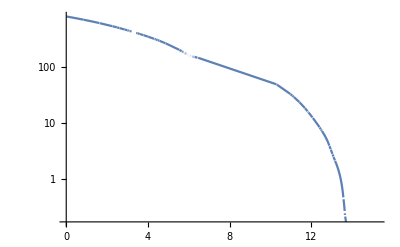

```mathematica
{m,n}={123,124};
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
σs=Diagonal[S];r=Length[σs];
σs=RandomVariate[MixtureDistribution[{1,3,1}, {NormalDistribution[12,1],NormalDistribution[6,0.2],NormalDistribution[3,1]}],123]
f[t_]:=Total[ Map[Max[#,0]&,σs-t]]
LogPlot[f[t],{t,0,1.1 Max[σs]}]
```

```mathematica
{m,n}={123,124};
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
σs=Diagonal[S];r=Length[σs];

vars=Table[s[i],{i,1,r}];
t=3;β=1.6^2; rOpt=Count[Sign[σs-t],1];
{MinVal,MinArg}=Minimize[ {
0.5(vars-σs).(vars-σs) +t Total[vars],
{vars>0,0.5 vars.vars>β}},vars] ;
{MinVal,MinArg=Chop[vars/.MinArg,10^-7]};
Ss=Join[Table[σs⟦i⟧-t,{i,1,rOpt}],ConstantArray[0,r-rOpt]];
α=√(β/(0.5 Ss.Ss));
Ss=α Ss
TableForm[{MinArg,Ss},
TableHeadings->{{"Numerical","Analytical"},Automatic}]
```

{1.95366,1.06025,0.366794,0.211086,0.,0.,0.,0.,0.,0.,0.}

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
Numerical | 1.95366 | 1.06025 | 0.366795 | 0.211087 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Analytical | 1.95366 | 1.06025 | 0.366794 | 0.211086 | 0. | 0. | 0. | 0. | 0. | 0. | 0.